```mathematica
zamianaRB[a_,b_,x_,k_]:=Module[{int, frac,re,n,m,p,q},
n=Max[
Length[IntegerDigits[a,2]],
Length[IntegerDigits[b,2]]];(*ilosc miejsc na czesci calkowiej*)
m=Length[IntegerDigits[10^k,2]];
(*calkowitych tyle ile najwieksza z przedzialu, po przecinku ile zadane w k*)
(*Kazdy dopelnia do n, po przecinku do k i zwraca jako ciag dl n+k*)
p=IntegerDigits[IntegerPart[x],2,n];(*calkowita wartosc*)
q=IntegerDigits[10^k*Round[FractionalPart[x],10^-k],2,m];
(*czesc ulamkowa*)
Join[p,q]
]
```

```mathematica
zamianaBR[a_,b_,x_,k_]:=Module[{n,m,p,q,int,frac},
n=Max[
Length[IntegerDigits[a,2]],
Length[IntegerDigits[b,2]]];
m=Length[IntegerDigits[10^k,2]];
(*Print["x: ",x];
Print[pocz];*)
(*czesc calkowita binarnie*)
p=Table[0,{n}];
For[i=1,i<n,i++,p⟦i⟧=x⟦i⟧];
(*czesc niecalkowita binarnie*)
q=Table[0,{m}];
For[i=1,i<m,i++,q⟦i⟧=x⟦i+n⟧];
(*Print["n: ",n,", m:",m, " p: ",p, " q: ",q, " x : ",x];*)
int=FromDigits[p,2];
frac=(10^-k)*FromDigits[q,2];
(*Print["w: ",int+frac*1.];
Print[kon];*)
int+frac*1.

]
```

## cGA

uczenie się na podstawie najlepszego i najgorszego osobnika wg wzoru
p_i=Piecewise[{{p_i+1/N, x_i=1 i y_i=0}, {p_i-1/N, x_i=0 i y_i=1}, {p_i, pozostale}}]    ,  x- najlepszy osobnik, y-najgorszy

```mathematica
Clear[cGA,valuate,compareW,compareB];
```

```mathematica
(*funkcja zliczająca jedynki*)
valuate[x_]:=Module[{val=0, n= Length[x],i=0,j=0,k=0},
For[i=1,i<=n,i++,val+=x⟦i⟧];
val];
(*n-dł osobnika, f-funkcja optymalizowana, size-rozmiar populacji, max-rzeczywiste maximum funkcji ({x,y}), itmax - ilość iteracji, która kończy algorytm
na przedziale [a,b], 10^(-dokl), qmax-ilosc identycznych wynikow pod rzad, ktora konczy alg*)
cGARE[f_,size_,maxT_,itmax_,a_,b_,dokl_,qmax_]:=Module[{P,best,q=0,worst,n=0,oldbest,max=maxT⟦2⟧,population,iter=1,k,wynik=Table[{0,0},{1}]},
(*generacja pop startowej*)
SeedRandom[];
n=Max[Length[IntegerDigits[a,2]],Length[IntegerDigits[b,2]]];
k=Length[IntegerDigits[10^dokl,2]];
P=Table[0.5,{n+k}];
population=Table[Table[0,{n+k}],{size}];
aBin=zamianaRB[a,b,a,dokl];
bBin=zamianaRB[a,b,b,dokl];
(*Porównywanie wartości funkcji dla osobników B-zwraca wiekszy, W-mniejszy*)
compareB[x1_,y_]:=If[
(f/.x->(zamianaBR[a,b,x1,dokl]))>(f/.x->(zamianaBR[a,b,y,dokl])),x1,y];
compareW[x1_,y_]:=If[
(f/.x->(zamianaBR[a,b,x1,dokl]))<(f/.x->(zamianaBR[a,b,y,dokl])),x1,y];
(*gdy przekroczy przedzial przyjmuje skrajna wartosc*)
przytnij[x_]:=
If[(zamianaBR[a,b,x,dokl])>b,bBin, 
If[(zamianaBR[a,b,x,dokl])<a,aBin,x]
];
For[j=1,j≤size,j++,
For[i=1,i≤n+k,i++,
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
];
population⟦j⟧=przytnij[population⟦j⟧];
];
(*ustalenie najlepszego osobnika z populacji*)
best=population⟦1⟧;
worst=best;
(*Algorytm kończy działanie po osiągnięciu max albo ilości iteracji*)

While[((f/.x->(zamianaBR[a,b,best,dokl]))≠max  && iter≠itmax&& qmax≠ q),
oldbest=best;
(*wyszukiwanie najlepszego osobnika*)
For[i=1,i≤size,i++,best=compareB[population⟦i⟧,best]];
(*wyszukiwanie najgorszego*)
For[i=1,i≤size,i++,worst=compareW[population⟦i⟧,worst]];
If[oldbest==best,q++,q=0];
(*Print["best:",best," iter: ",iter];*)
wynik⟦iter⟧={iter,f/.x->(zamianaBR[a,b,best,dokl])};
(*Obliczenie nowego wektora prawdopodobienstwa*)
For[i=1,i≤n+k,i++,
If[best⟦i⟧==1&&worst⟦i⟧==0,P⟦i⟧+=1/size,
If[best⟦i⟧==0 && worst⟦i⟧==1,P⟦i⟧-=1/size]]];
(*Gdy prawdopodobienstwo ujemne -> zamiana na 0, gdy większe od 1 na 1*)
For[i=1,i≤n+k,i++,If[P⟦i⟧<0,P⟦i⟧=0,P⟦i⟧=Mod[P⟦i⟧,1]]];
(*Generacja nowej populacji*)
For[j=1,j≤size,j++,
For[i=1,i≤n+k,i++,population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
]];

iter++;
wynik2=Table[{iter,f/.x->(zamianaBR[a,b,best,dokl])},{iter}];
For[i=1,i<iter,i++,wynik2⟦i⟧=wynik⟦i⟧];
wynik=wynik2;
];

Print["Maximum (",zamianaBR[a,b,best,dokl],", ",f/.x->zamianaBR[a,b,best,dokl],"), (rzeczywiste: ",maxT,") uzyskane po iteracjach: ",iter];
punkt={zamianaBR[a,b,best,dokl],f/.x->zamianaBR[a,b,best,dokl]};
(*Print[wynik];*)
Print[Show[Plot[f,{x,a,b}],ListPlot[{punkt},Filling->Axis,PlotStyle->Red]]];
ListLinePlot[wynik,PlotLabel->"Zbieżność do max"]
]
```

-(x-2)^2

```mathematica
(*cGARE[f_,size_,maxT_,itmax_,a_,b_,dokl_,qmax_]*)
```

cGA dla -(x-2)^2 na [0,10] dokładność 10^-4, populacja
 5os, max 200it, max 20 tych samych osobników

Maximum (2., 0.), (rzeczywiste: {2,0}) uzyskane po iteracjach: 5

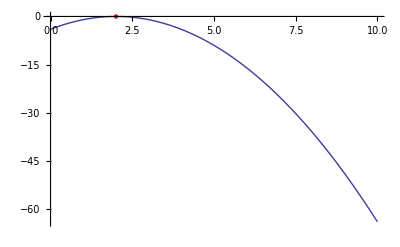

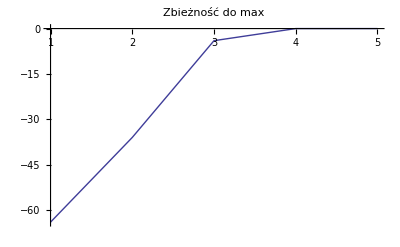

```mathematica
cGARE[-(x-2)^2,5,{2,0},200,0,10,4,20]
```

cGA dla -(x-2)^2 na [0,10] dokładność 10^-3, populacja
 50os, max 200it, max 20 tych samych osobników

Maximum (6., -16.), (rzeczywiste: {2,0}) uzyskane po iteracjach: 33

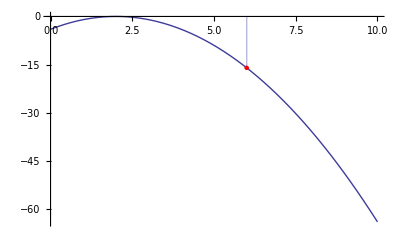

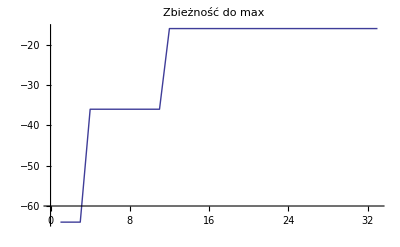

```mathematica
cGARE[-(x-2)^2,5,{2,0},200,0,10,3,20]
```

cGA dla -(x-2)^2 na [0,10] dokładność 10^-6, populacja
 5os, max 200it, max 40 tych samych osobników

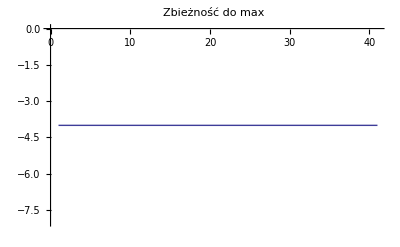

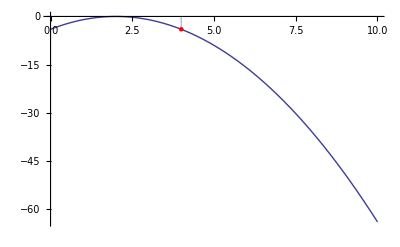

Maximum (4., -4.), (rzeczywiste: {2,0}) uzyskane po iteracjach: 41

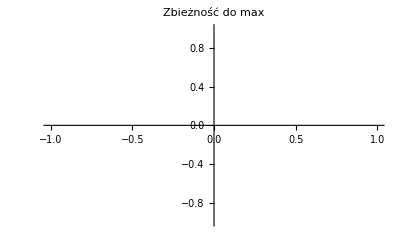

```mathematica
cGARE[-(x-2)^2,5,{2,0},200,0,10,6,40]
```

```mathematica
cGARE[-(x-2)^2,15,{2,0},200,0,10,3,40]
```

$Aborted

Wniosek - duza liczebnosc populacji, znacznie wydłuża pracę, bez widocznie lepszych efektów

| x | Sin[x] + | x |

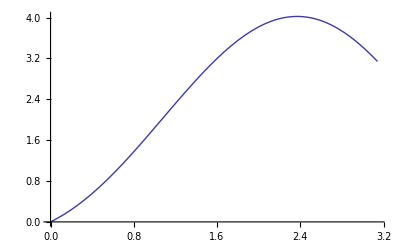

```mathematica
test1[x_]:=Abs[x]*Sin[x]+Abs[x];
Plot[test1[x],{x,0,π}]
```

cGA dla test1(x) na [0,π] dokładność 10^-6, populacja
 10os, max 300it, max 130 tych samych osobników

Maximum (2.51993, 3.9875), (rzeczywiste: {2.5,4}) uzyskane po iteracjach: 18

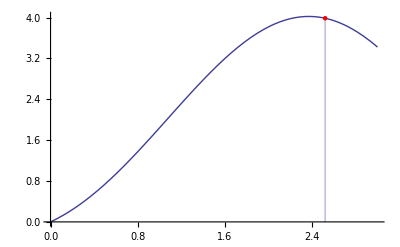

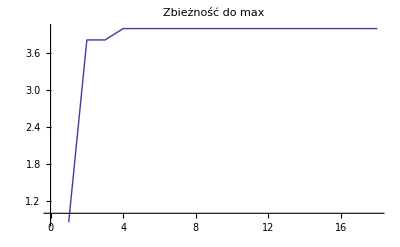

```mathematica
cGARE[test1[x],4,{2.5,4},300,0,3,6,13]
```

cGA dla test1(x) na [0,π] dokładność 10^-4, populacja
 10os, max 300it, max 130 tych samych osobników

Maximum (2.03, 3.8497), (rzeczywiste: {2.5,4}) uzyskane po iteracjach: 133

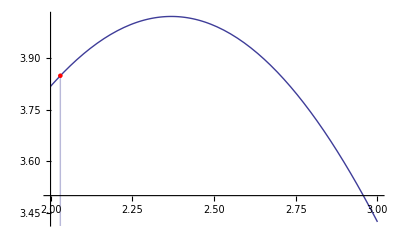

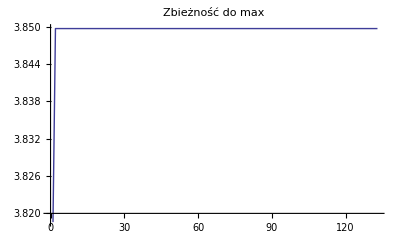

```mathematica
cGARE[test1[x],10,{2.5,4},300,2,3,4,130]
```

cGA dla test1(x) na [0,π] dokładność 10^-6, populacja
 10os, max 200it, max 130 tych samych osobników

Maximum (2.36858, 4.02255), (rzeczywiste: {2.5,4}) uzyskane po iteracjach: 300

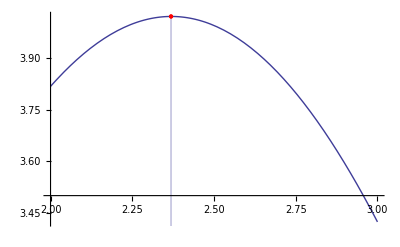

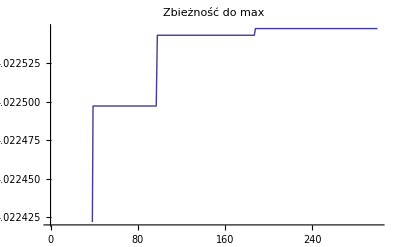

```mathematica
cGARE[test1[x],10,{2.5,4},300,2,3,6,130]
```

test2 (x)

test2(x)=|x| sin(x) + 1/10 x

```mathematica
P2=FindMaximum[test2[x],{x,0,π}]
```

{2.02442,{x→2.06531}}

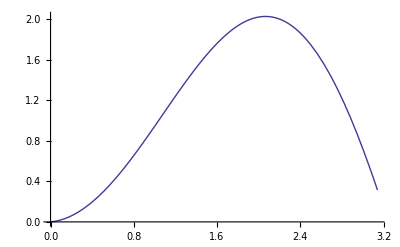

```mathematica
test2[x_]:=Abs[x]*Sin[x]+1/10 x;
Plot[test2[x],{x,0,Pi}]
```

cGA dla test2(x) na [0,π] dokładność 10^-4, populacja
 10os, max 200it, max 130 tych samych osobników

Maximum (2.3412, 1.91423), (rzeczywiste: {2.06531,2.02442}) uzyskane po iteracjach: 141

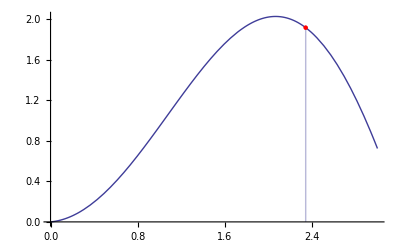

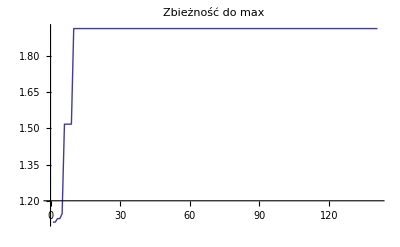

```mathematica
cGARE[test2[x],10,{P2[[2,1,2]],P2[[1]]},200,0,π,4,130]
```

cGA dla test2(x) na [0,π] dokładność 10^-4, populacja
 15os, max 200it, max 130 tych samych osobników

Maximum (2.0506, 2.02412), (rzeczywiste: {2.06531,2.02442}) uzyskane po iteracjach: 159

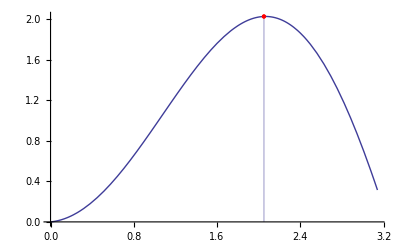

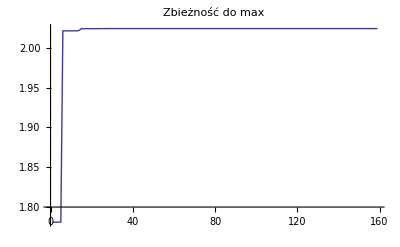

```mathematica
cGARE[test2[x],11,{P2[[2,1,2]],P2[[1]]},200,0,π,4,130]
```

test3 (x)

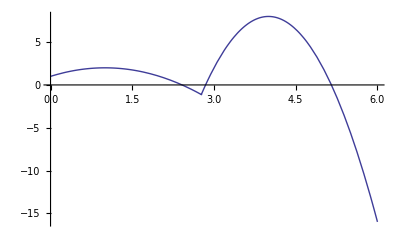

```mathematica
test3[x_]:=Module[{},If[0≤x≤2.773,-(x-1)^2+2,-6 (x-4)^2+8]];
Plot[test3[x],{x,0,6}]
```

```mathematica
P3=FindMaximum[-6 (x-4)^2+8,{x,3,6}];
```

cGA dla test3(x) na [0,6] dokładność 10^-4, populacja
 10os, max 200it, max 130 tych samych osobników

Maximum (0.2764, 1.4764), (rzeczywiste: {4.,8.}) uzyskane po iteracjach: 131

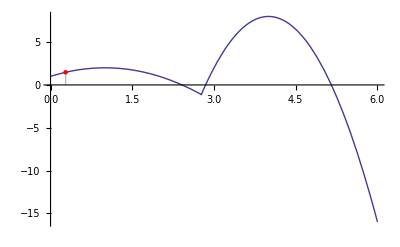

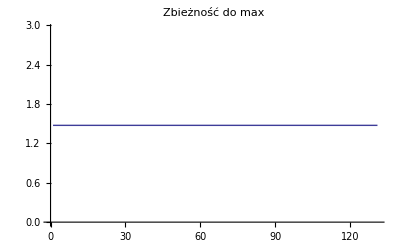

```mathematica
cGARE[test3[x],10,{P3⟦2,1,2⟧,P3⟦1⟧},200,0,6,4,130]
```

Wniosek: Wpadł w ekstremum lolalne

cGA dla test3(x) na [0,6] dokładność 10^-4, populacja
 10os, max 200it, max 130 tych samych osobników

Maximum (4.35, 7.265), (rzeczywiste: {4.,8.}) uzyskane po iteracjach: 89

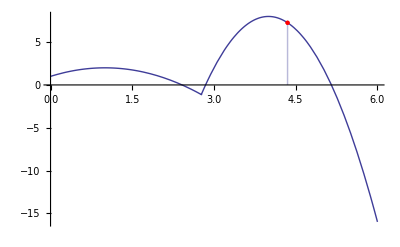

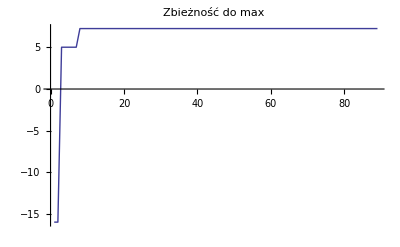

```mathematica
cGARE[If[0≤x≤2.773,-(x-1)^2+2,-6 (x-4)^2+8],10,{4.000000000011882,8.},200,0,6,4,80]
```

cGA dla test3(x) na [0,6] dokładność 10^-4, populacja
 10os, max 200it, max 130 tych samych osobników

Maximum (4.2182, 7.71433), (rzeczywiste: {4.,8.}) uzyskane po iteracjach: 84

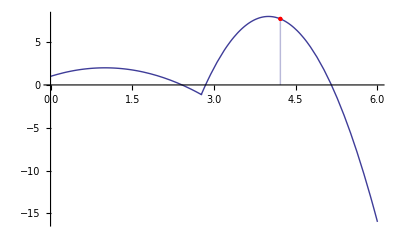

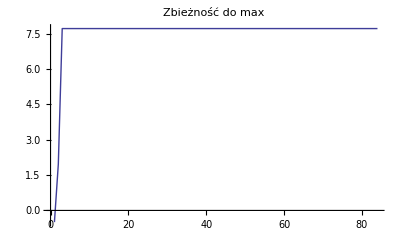

```mathematica
cGARE[If[0≤x≤2.773,-(x-1)^2+2,-6 (x-4)^2+8],10,{4.000000000011882,8.},200,0,6,4,80]
```

```mathematica
test5(x)
```

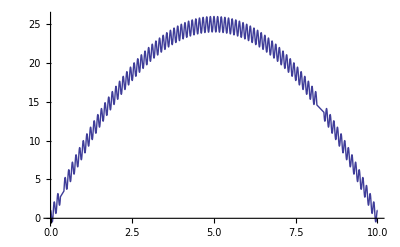

```mathematica
test5[x_]:=-(x-5)^2+Cos[18Pi (x-5)]+25;Plot[test5[x],{x,0,10},AxesOrigin->{0,0}]
```

cGA dla test5(x) na [0,10] dokładność 10^-4, populacja
 10os, , max 300it, max 40 tych samych osobników

Maximum (2.9628, 20.3419), (rzeczywiste: {5.,26}) uzyskane po iteracjach: 46

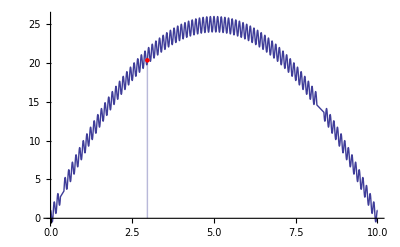

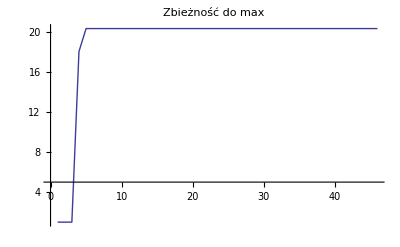

```mathematica
cGARE[test5[x],10,{5.,26},300,0,10,4,40]
```

cGA dla test5(x) na [0,10] dokładność 10^-4, populacja
 10os, max 300it, max 40 tych samych osobników

Maximum (5.2086, 25.6742), (rzeczywiste: {5.,26}) uzyskane po iteracjach: 47

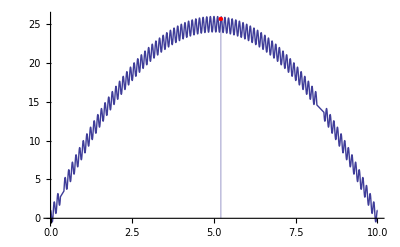

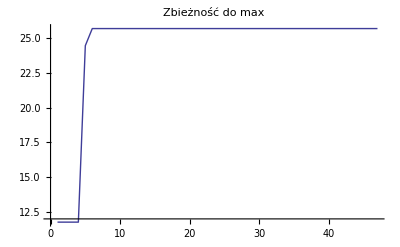

```mathematica
cGARE[test5[x],10,{5.,26},300,0,10,4,40]
```

cGA dla test5(x) na [0,10] dokładność 10^-6, populacja
 10os,  max 300it, max 40 tych samych osobników

Maximum (0.487354, 3.88101), (rzeczywiste: {5.,26}) uzyskane po iteracjach: 44

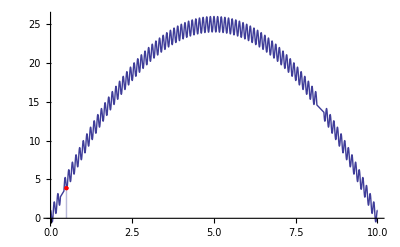

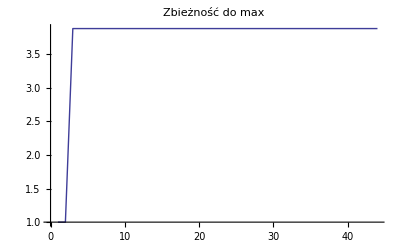

```mathematica
cGARE[test5[x],10,{5.,26},300,0,10,6,40]
```

cGA dla test5(x) na [0,10] dokładność 10^-6, populacja
 10os,  max 300it, max 40 tych samych osobników

Maximum (2.81824, 19.5827), (rzeczywiste: {5.,26}) uzyskane po iteracjach: 45

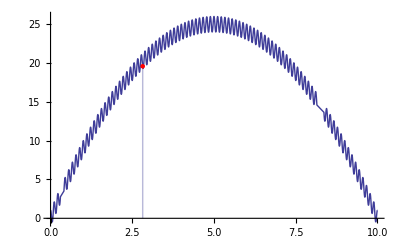

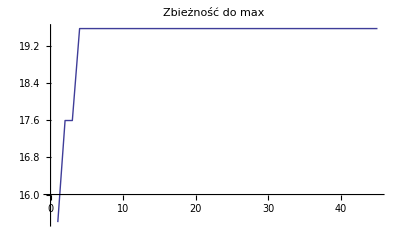

```mathematica
cGARE[test5[x],10,{5.,26},300,0,10,6,40]
```

cGA dla test5(x) na [0,10] dokładność 10^-3, populacja
 10os,  max 300it, max 40 tych samych osobników

Maximum (4.988, 25.7783), (rzeczywiste: {5.,26}) uzyskane po iteracjach: 43

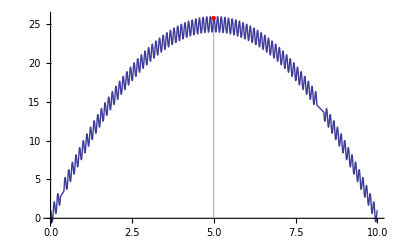

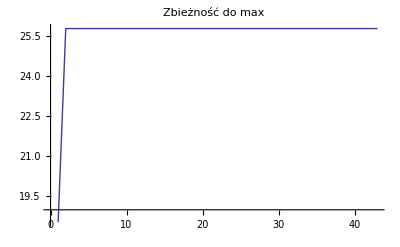

```mathematica
cGARE[test5[x],10,{5.,26},300,0,10,3,40]
```